```mathematica
sampleNull=Map[#[[1,2]]&,Tally[Table[{Norm[Map[Length,allGraphs5[k,"vertexsets"]]],k},{k,allGraphs5NullAtomKeys}],#1[[1]]==#2[[1]]&]]
```

{0,39366,52974,57528,59048,52976,39384}

```mathematica
sampleFull=Map[#[[1,2]]&,Tally[Table[{Norm[Map[Length,allGraphs5[k,"vertexsets"]]],k},{k,allGraphs5AtomKeys}],#1[[1]]==#2[[1]]&]]
```

{29524,29525,29537,29560,29888,30586,59048}

## Let' s highlight cycles

```mathematica
ChangeCycleSymbol[s_]:=Symbol[StringReplace[SymbolName[s],"c"->"n"]]
```

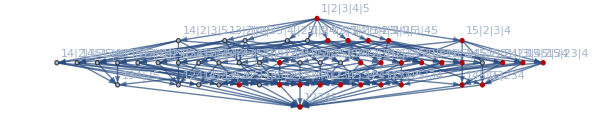
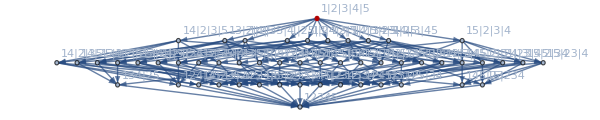
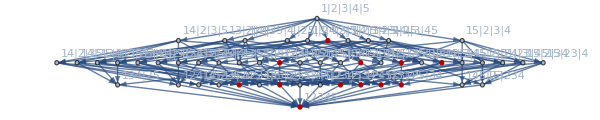
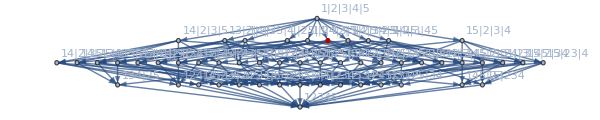
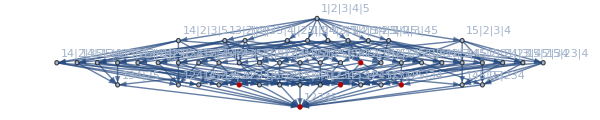
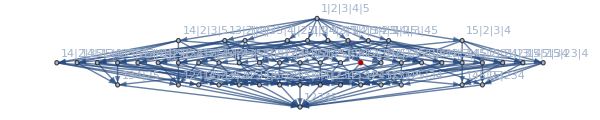
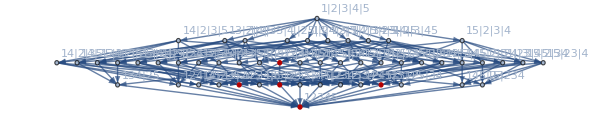
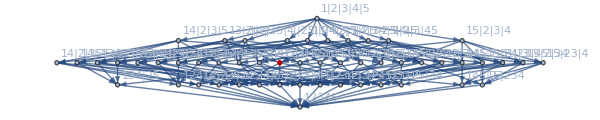
{-Graphics-0→{c12345+c1234x5+c1235x4+c123x45+c123x4x5+c1245x3+c125x34+c125x3x4+c12x345+c12x34x5+c12x3x45+c12x3x4x5+c1345x2+c145x23+c145x2x3+c15x234+c15x23x4+c15x2x34+c15x2x3x4+c1x2345+c1x234x5+c1x23x45+c1x23x4x5+c1x2x345+c1x2x34x5+c1x2x3x45+c1x2x3x4x5,-Graphics-,-Graphics-},-Graphics-39366→{c12345+c1234x5+c1235x4+c123x45+c123x4x5+c1245x3+c125x34+c125x3x4+c12x345+c12x34x5+c12x3x45+c12x3x4x5,-Graphics-,-Graphics-},-Graphics-39384→{c12345+c1234x5+c125x34+c12x345+c12x34x5,-Graphics-,-Graphics-},-Graphics-52974→{c12345+c1234x5+c1235x4+c123x45+c123x4x5,-Graphics-,-Graphics-},-Graphics-52976→{c12345+c123x45,-Graphics-,-Graphics-},-Graphics-57528→{c12345+c1234x5,-Graphics-,-Graphics-},-Graphics-59048→{c12345,-Graphics-,-Graphics-}}

```mathematica
Table[
Framed[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]]->
With[{mysyms=Map[ChangeCycleSymbol, ListofVars[(allGraphs5[k,"colofour"]/.cyclesols)]]},
{allGraphs5[k,"colofour"]/.cyclesols,Graph[MobiusGraphSimple[K5Key,allGraphs5],GraphHighlight->mysyms],
Graph[MobiusGraphSimple[K5Key,allGraphs5],GraphHighlight->Map[ChangeAnySymbol,ListofVars[allGraphs5[k,"colofourrealnull"]]]]
}
]
,
{k,Sort[sampleNull,CompareSymbols[allGraphs5[#1,"colofourrealnull"],allGraphs5[#2,"colofourrealnull"]]&]}
]
```

## Let' s highlight trees

```mathematica
ChangeTreeSymbol[s_]:=Symbol[StringReplace[SymbolName[s],"v"->"n"]]
```

```mathematica
Sort[allGraphs5NullAtomKeys,CompareSymbols[allGraphs5[#1,"colofourrealnull"],allGraphs5[#2,"colofourrealnull"]]&]
```

{0,2,18,6,486,162,54,39366,13122,4374,1458,26,488,666,546,168,218,72,39368,39384,39372,52974,43902,40878,13124,13284,13176,17514,14586,4380,4860,4428,5834,1476,1944,1620,728,39392,52976,57528,54492,43908,45416,40896,13340,17568,18980,14748,4920,6320,2124,59048}

```mathematica
allGraphs5[0,"colofour"]
```

v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5

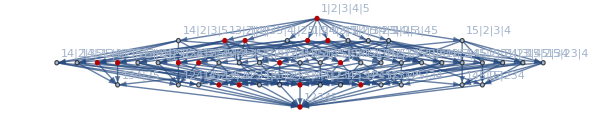
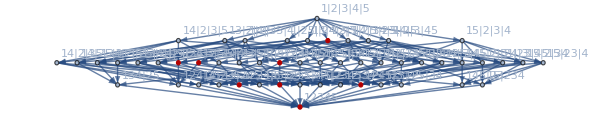
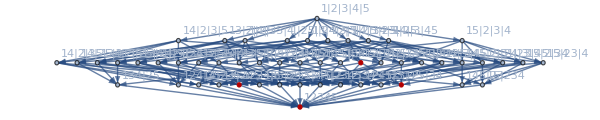
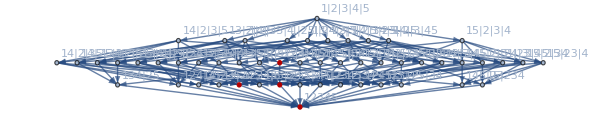
{-Graphics-0→{t12345+t1234x5+t123x4x5+t1245x3+t124x3x5+t12x35x4+t12x3x4x5+t1345x2+t134x2x5+t13x245+t13x25x4+t13x2x4x5+t1x245x3+t1x24x3x5+t1x2x35x4+t1x2x3x4x5,-Graphics-,-Graphics-},-Graphics-39366→{t12345+t1234x5+t1235x4+t123x4x5+t1245x3+t124x3x5+t12x35x4+t12x3x4x5,-Graphics-,-Graphics-},-Graphics-39384→{t12345+t1234x5+t125x34+t12x34x5,-Graphics-,-Graphics-},-Graphics-52974→{t12345+t1234x5+t1235x4+t123x4x5,-Graphics-,-Graphics-},-Graphics-52976→{t12345+t123x45,-Graphics-,-Graphics-},-Graphics-57528→{t12345+t1234x5,-Graphics-,-Graphics-},-Graphics-59048→{t12345,-Graphics-,-Graphics-}}

```mathematica
Table[
Framed[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]]->
With[{mysyms=Map[ChangeTreeSymbol, ListofVars[(allGraphs5[k,"colofour"]/.sols2)]]},
{allGraphs5[k,"colofour"]/.sols2,Graph[MobiusGraphSimple[K5Key,allGraphs5],GraphHighlight->mysyms],
Graph[MobiusGraphSimple[K5Key,allGraphs5],GraphHighlight->ListofVars[allGraphs5[k,"colofourrealnull"]]]
}
],
{k,Sort[sampleNull,CompareSymbols[allGraphs5[#1,"colofourrealnull"],allGraphs5[#2,"colofourrealnull"]]&]}
]
```

## Trees and complete base

```mathematica
ChangeAnySymbol[s_]:=Symbol[StringReplace[SymbolName[s],StringTake[SymbolName[s],1]->"n"]]
```

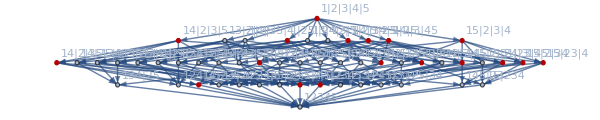
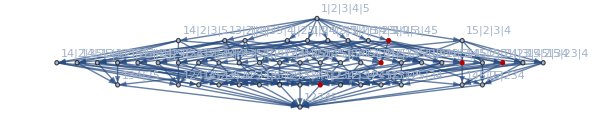
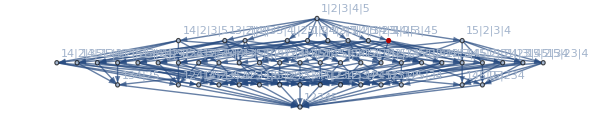
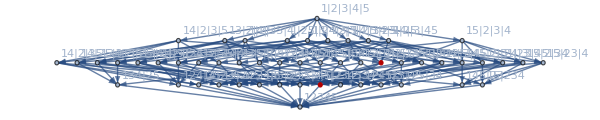
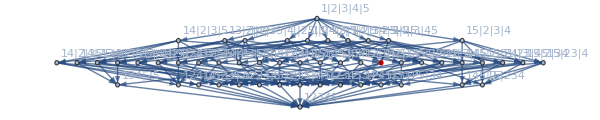
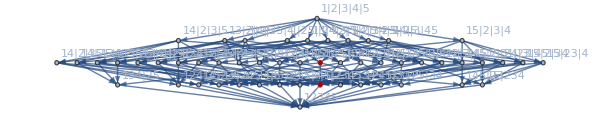
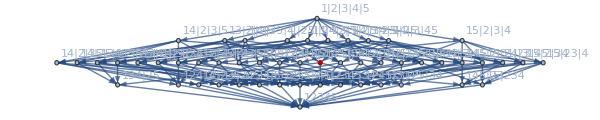
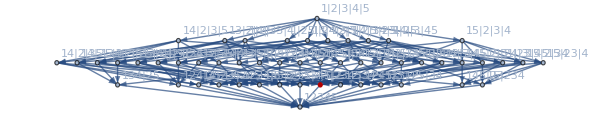
{-Graphics-29524→{-t1345x2+2 t145x2x3+t14x235+t14x2x35-t14x2x3x5+t15x23x4+t15x2x34-t15x2x3x4-6 t1x2345+2 t1x234x5+t1x235x4+t1x23x45-t1x23x4x5-t1x25x3x4+2 t1x2x345-t1x2x34x5-t1x2x3x45+t1x2x3x4x5,-Graphics-,-Graphics-},-Graphics-29525→{-t145x2x3+2 t1x2345-t1x23x45-t1x2x345+t1x2x3x45,-Graphics-,-Graphics-},-Graphics-29537→{-t1x2345+t1x2x345,-Graphics-,-Graphics-},-Graphics-29560→{-t1x2345+t1x25x34,-Graphics-,-Graphics-},-Graphics-29888→{t1x2345,-Graphics-,-Graphics-},-Graphics-30586→{t15x234,-Graphics-,-Graphics-},-Graphics-59048→{t12345,-Graphics-,-Graphics-}}

```mathematica
Table[
Framed[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]]->
With[{mysyms=Map[ChangeAnySymbol, ListofVars[(allGraphs5[k,"colofour"]/.sols2)]]},
{(allGraphs5[k,"colofour"]/.sols2),Graph[MobiusGraphSimple[K5Key,allGraphs5],GraphHighlight->mysyms],
Graph[MobiusGraphSimple[K5Key,allGraphs5],GraphHighlight->Map[ChangeAnySymbol,ListofVars[allGraphs5[k,"colofour"]]]]
}
],
{k,Sort[sampleFull,CompareSymbols[allGraphs5[#1,"colofour"],allGraphs5[#2,"colofour"]]&]}
]
```